#### Define fields, metric, potential, parameters

```mathematica
nf=3;
f=Table[Symbol["f"<>ToString[i]][t],{i,nf}];
{σ,θ,χ}=f;

df=Table[Symbol["f"<>ToString[i]]'[t],{i,nf}](*f[[#]]'[t]&/@Table[n,{n,1,nf}]*);
ddf=Table[Symbol["f"<>ToString[i]]''[t],{i,nf}];

G=({{1, 0, 0}, {0, (1+ξ σ)^2, 0}, {0, 0, (1+ξ σ)^2}});
Ginv=Inverse[G];

dfNorm2=Simplify[df.G.df];
dfNorm=Simplify@Sqrt[dfNorm2];
sig=df/dfNorm;
K=1/2 dfNorm2;

gBCH=1+ξ σ;
V=Λ(2-Subscript[C, 2] θ^2-Subscript[C, 3] χ^2+Subscript[C, 1](1-Exp[-σ^2/Σ^2]));
(*V=U[σ,θ,χ];*)
Vfn[σ_,θ_,χ_]:=V=Λ(2-Subscript[C, 2] θ^2-Subscript[C, 3] χ^2+Subscript[C, 1](1-Exp[-σ^2/Σ^2]));
```

```mathematica
Vgrad=Grad[V,f];
VgradUp=Ginv.Vgrad;
Vhess=D[V,{f,2}];
Vsig=sig.Vgrad;

H=Sqrt[(K+V)/3];
eH=K/H^2;
```

#### Geometric objects and mass matrix

```mathematica
csymb:=Simplify@Table[1/2 Sum[Ginv[[i,m]](D[G[[m,k]],f[[j]]]+D[G[[j,m]],f[[k]]]-D[G[[j,k]],f[[m]]]),{m,nf}],{i,nf},{j,nf},{k,nf}];
riemann:=Simplify@Table[D[csymb[[i,j,k]],f[[l]]]-D[csymb[[i,j,l]],f[[k]]]+Sum[csymb[[m,j,k]]csymb[[i,l,m]],{m,nf}]-Sum[csymb[[m,j,l]]csymb[[i,k,m]],{m,nf}],{i,nf},{j,nf},{l,nf},{k,nf}];
ricciT:=Table[Sum[riemann[[i,j,i,k]],{i,nf}],{j,nf},{k,nf}];
ricciS:=Sum[(Ginv.ricciT)[[i,i]],{i,nf}];
```

```mathematica
csymb//MatrixForm
(*ricciS*)
```

((0
0
0) | (0
-ξ (1+ξ f1[t])
0) | (0
0
-ξ (1+ξ f1[t]))
(0
ξ/(1+ξ f1[t])
0) | (ξ/(1+ξ f1[t])
0
0) | (0
0
0)
(0
0
ξ/(1+ξ f1[t])) | (0
0
0) | (ξ/(1+ξ f1[t])
0
0))

```mathematica
ricciS
```

-(2 ξ^2)/(1+ξ f1[t])^2

```mathematica
Ddf=ddf+Table[Sum[csymb[[i,j,k]]df[[j]]df[[k]],{j,nf},{k,nf}],{i,nf}];
wVec=D[sig,t]+Table[Sum[csymb[[i,j,k]]df[[j]]sig[[k]],{j,nf},{k,nf}],{i,nf}];
w2=wVec.G.wVec;
w=Simplify@Sqrt[w2];
s=Simplify[wVec/w];
```

```mathematica
DdV=Vhess-Table[Sum[csymb[[i,j,k]]Vgrad[[i]],{i,nf}],{j,nf},{k,nf}];
massMx=Ginv.DdV-Table[Sum[riemann[[i,l,m,j]]df[[l]]df[[m]],{l,nf},{m,nf}],{i,nf},{j,nf}];
mSigSig=sig.G.massMx.sig;
mss=s.G.massMx.s;
```

```mathematica
eom=Simplify[Ddf+3H df+VgradUp];
(*eomBCH =Simplify[ eom/.{V->vBCH}];*)
```

```mathematica
eom//MatrixForm
(*eomBCH//MatrixForm*)
```

((2 ⅇ^(-f1[t]^2/Σ^2) Λ f1[t] C_1)/Σ^2-ξ (1+ξ f1[t]) f2'[t]^2-ξ (1+ξ f1[t]) f3'[t]^2+√(3/2) f1'[t] √(2 Λ (2+(1-ⅇ^(-f1[t]^2/Σ^2)) C_1-f2[t]^2 C_2-f3[t]^2 C_3)+f1'[t]^2+(1+ξ f1[t])^2 (f2'[t]^2+f3'[t]^2))+f1''[t]
-(2 Λ f2[t] C_2)/(1+ξ f1[t])^2+(2 ξ f1'[t] f2'[t])/(1+ξ f1[t])+√(3/2) f2'[t] √(2 Λ (2+(1-ⅇ^(-f1[t]^2/Σ^2)) C_1-f2[t]^2 C_2-f3[t]^2 C_3)+f1'[t]^2+(1+ξ f1[t])^2 (f2'[t]^2+f3'[t]^2))+f2''[t]
-(2 Λ f3[t] C_3)/(1+ξ f1[t])^2+(2 ξ f1'[t] f3'[t])/(1+ξ f1[t])+√(3/2) f3'[t] √(2 Λ (2+(1-ⅇ^(-f1[t]^2/Σ^2)) C_1-f2[t]^2 C_2-f3[t]^2 C_3)+f1'[t]^2+(1+ξ f1[t])^2 (f2'[t]^2+f3'[t]^2))+f3''[t])

#### Solve background equations of motion

```mathematica
Λval=3.99*^-1(*-13*);
Σval=0.775;
ξval=3.32/Σval;
C1val=10;
C2val=0.0476;
C3val=0.01;
σi=2.12;
θi=9.84*^-3;
χi=8*^-3;
```

```mathematica
(*Plot3D[Vfn[σ,θ]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval},{σ,-1,3},{θ,-2,2}]*)
```

```mathematica
tEnd=1*^2;
soln=NDSolve[{Evaluate[eom[[1]]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}]==0,Evaluate[eom[[2]]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}]==0,Evaluate[eom[[3]]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}]==0,f1[0]==σi,f2[0]==θi,f3[0]==χi,f1'[0]==0,f2'[0]==0,f3'[0]==0},{f1,f2,f3},{t,0,tEnd}(*,MaxSteps->Infinity,WorkingPrecision->30,InterpolationOrder->All*)]
```

{{f1→InterpolatingFunction[…],f2→InterpolatingFunction[…],f3→InterpolatingFunction[…]}}

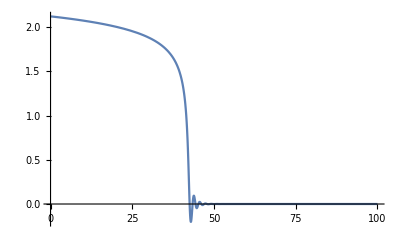

```mathematica
Plot[Evaluate[f1[t]/.soln],{t,0,tEnd}]
```

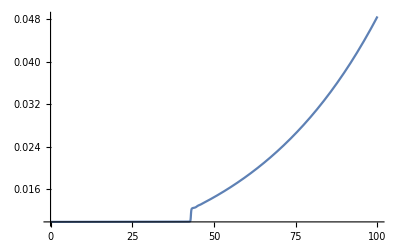

```mathematica
Plot[Evaluate[f2[t]/.soln],{t,0,tEnd}]
```

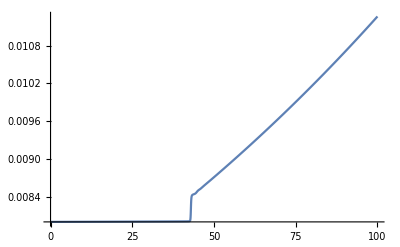

```mathematica
Plot[Evaluate[f3[t]/.soln],{t,0,tEnd}]
```

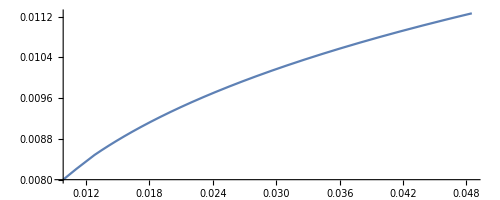

```mathematica
ParametricPlot[Evaluate[{θ,χ}/.soln],{t,0,tEnd},AspectRatio->Full]
```

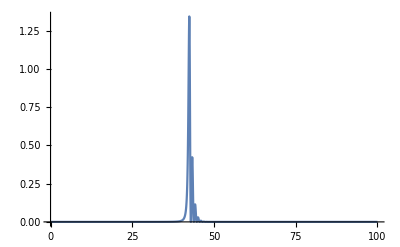

```mathematica
Plot[Evaluate[eH//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}/.soln],{t,0,tEnd},PlotRange->All]
```

```mathematica
(*infEnd=FindRoot[Evaluate[eH//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Λ->Λval,ξ->ξval}/.soln]-1,{t,tEnd*0.8}]*)
```

```mathematica
(*Ninf=NIntegrate[Evaluate[H//.{g->gEGNO,V->vEGNO,a->0.5,c->1000,m->1}/.soln],{t,0,t/.infEnd}]*)
```

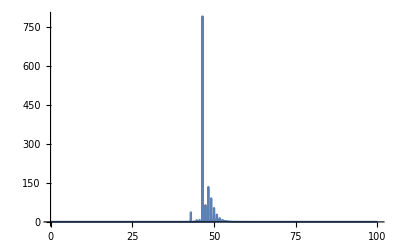

```mathematica
Plot[Evaluate[w/H//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}/.soln],{t,0,tEnd(*t/.infEnd*)},PlotRange->All]
```

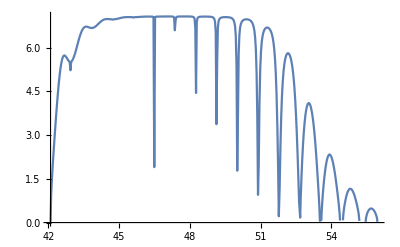

```mathematica
Plot[Evaluate[Sqrt[(sig.DdV.sig)/H^2]]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}/.soln,{t,0,tEnd(*t/.infEnd*)},PlotRange->All]
```

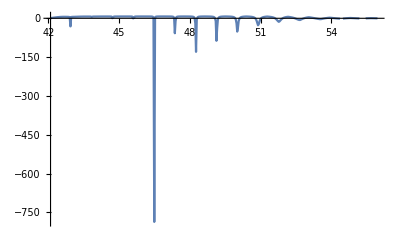

```mathematica
Plot[Evaluate[Sqrt[(sig.DdV.sig)/H^2]-w/H]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}/.soln,{t,0,tEnd(*t/.infEnd*)},PlotRange->All]
```

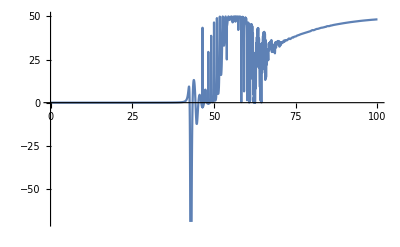

```mathematica
Plot[Evaluate[mss/H^2]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}/.soln,{t,0,tEnd(*t/.infEnd*)},PlotRange->Automatic]
```

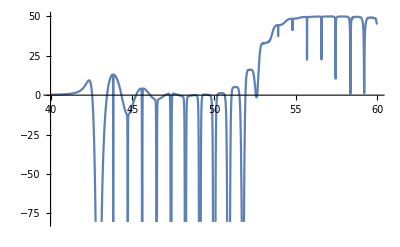

```mathematica
Plot[Evaluate[(mss-w^2)/H^2]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}/.soln,{t,tEnd*0.4,tEnd*0.6(*t/.infEnd*)},PlotRange->Automatic]
```

#### Smooth out oscillatory features in trajectory

```mathematica
Plot[Evaluate[f1[t]/.soln],{t,0,tEnd}]
```

-Graphics-

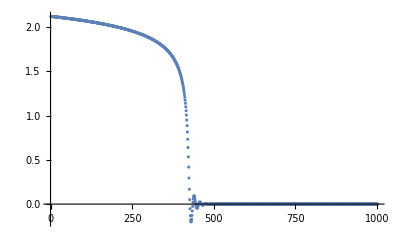

```mathematica
f1List=Table[{t,#} & /@(f1[t]/.soln[[1,1]]),{t,0,tEnd,0.1}];
ListPlot[Transpose@f1List,PlotRange->All]
```

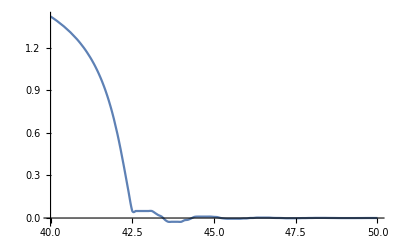

```mathematica
f1smoothShifted=Interpolation[MedianFilter[f1List,tEnd/10]];
f1smoothFn[t_]:=f1smoothShifted[10t+1];
f1smooth=f1smoothFn[t];
Plot[f1smooth,{t,tEnd*0.4,tEnd*0.5}]
```

```mathematica
f1smooth
```

InterpolatingFunction[…][1+10 t]

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

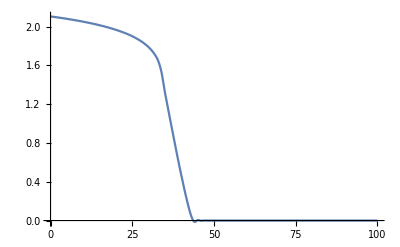

```mathematica
f1smoothAvg=Interpolation[MovingAverage[f1List,tEnd/10]];
Plot[f1smoothAvg[t],{t,0,tEnd}]
```

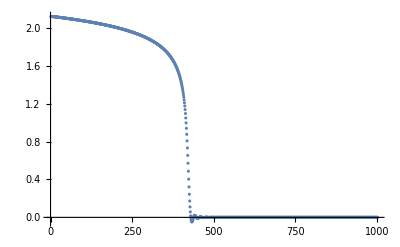

```mathematica
f1smoothGaussList=GaussianFilter[f1List,10];
ListPlot[f1smoothGaussList]
f1smoothGauss=Interpolation[f1smoothGaussList];
(*f1smoothFn[t_]:=f1smoothShifted[10t+1];
f1smooth=f1smoothFn[t];*)
(*Plot[f1smoothGauss,{t,0,tEnd}]*)
```

```mathematica
(*T=5;
f1avg:=NIntegrate[Evaluate[f1[t+x]/.soln]/T,{x,-T/2,T/2}];*)
```

```mathematica
(*Plot[f1avg,{t,0,tEnd}]*)
```

```mathematica
(*fn[x_]:=Sin[x]+Cos[20x]/10;*)
```

```mathematica
(*Plot[fn[x],{x,0,2Pi},PlotRange->All]*)
```

```mathematica
(*L=0.3;
fnAvg=Integrate[fn[x+t]/L,{t,-L/2,L/2}];*)
(*fnAvg=Integrate[fn[x] Exp[-(x-t)^2/(2*0.1)]/(√(2Pi*0.1)),{t,-Infinity,Infinity}];*)
```

```mathematica
(*Plot[{1,fnAvg},{x,0,2Pi}]*)
```

#### Compute dynamics for smoothed trajectory

```mathematica
σFake=f1smooth;
θFake=f2[t]/.soln[[1,2]];
χFake=f3[t]/.soln[[1,3]];
σdFake=D[σFake,t];
θdFake=D[θFake,t];
χdFake=D[χFake,t];
velFake={σdFake,θdFake,χFake};
```

```mathematica
σFake
```

InterpolatingFunction[…][1+10 t]

```mathematica
χFake
```

InterpolatingFunction[…][t]

```mathematica
velFake
```

{10 InterpolatingFunction[…][1+10 t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
Gfake=G/.{σ->σFake};
sigFake=Simplify[velFake/Sqrt[velFake.Gfake.velFake]];
```

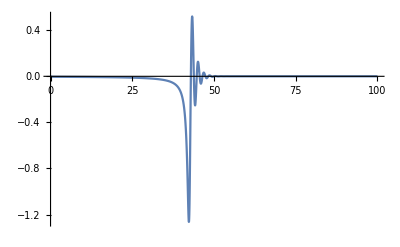

```mathematica
Plot[f1'[t]/.soln,{t,0,tEnd},PlotRange->All]
```

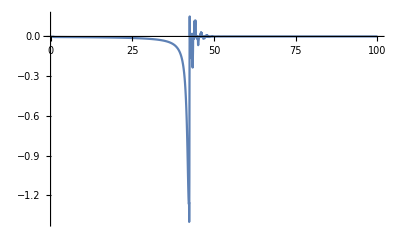

```mathematica
Plot[σdFake,{t,0,tEnd},PlotRange->All]
```

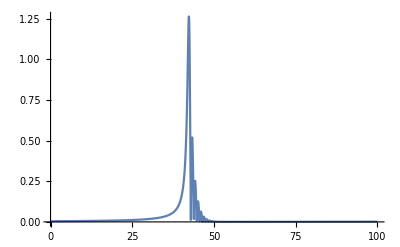

```mathematica
Plot[dfNorm/.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}/.soln,{t,0,tEnd},PlotRange->All]
```

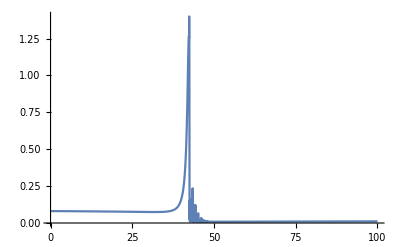

```mathematica
Plot[Sqrt[velFake.Gfake.velFake]/.ξ->ξval,{t,0,tEnd},PlotRange->All]
```

```mathematica
Gfake//MatrixForm
```

(1 | 0 | 0
0 | (1+ξ InterpolatingFunction[…][1+10 t])^2 | 0
0 | 0 | (1+ξ InterpolatingFunction[…][1+10 t])^2)

```mathematica
wVecFake=Simplify[(D[sigFake,t]+Table[Sum[csymb[[i,j,k]]velFake[[j]]sigFake[[k]],{j,nf},{k,nf}],{i,nf}])/.{σ->σFake}];
```

```mathematica
Hfake=Sqrt[(1/2 velFake.Gfake.velFake+V/.{σ->σFake,θ->θFake,χ->χFake})/3];
```

```mathematica
Plot[Evaluate[w/H//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}/.soln],{t,0,tEnd(*t/.infEnd*)},PlotRange->All]
```

-Graphics-

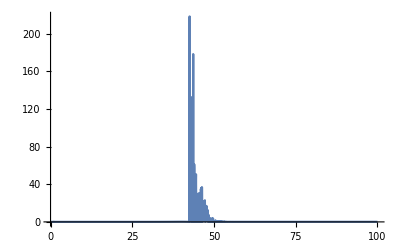

```mathematica
Plot[Sqrt[wVecFake.Gfake.wVecFake]/Hfake/.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval},{t,0,tEnd},PlotRange->All]
```

```mathematica
sFake=wVecFake/Sqrt[wVecFake.Gfake.wVecFake];
```

```mathematica
massMx//MatrixForm
```

((2 ⅇ^(-f1[t]^2/Σ^2) Λ C_1)/Σ^2-(4 ⅇ^(-f1[t]^2/Σ^2) Λ f1[t]^2 C_1)/Σ^4 | (2 Λ ξ f2[t] C_2)/(1+ξ f1[t]) | (2 Λ ξ f3[t] C_3)/(1+ξ f1[t])
(2 Λ ξ f2[t] C_2)/(1+ξ f1[t])^3 | ((2 ⅇ^(-f1[t]^2/Σ^2) Λ ξ f1[t] (1+ξ f1[t]) C_1)/Σ^2-2 Λ C_2)/(1+ξ f1[t])^2-ξ^2 f3'[t]^2 | ξ^2 f2'[t] f3'[t]
(2 Λ ξ f3[t] C_3)/(1+ξ f1[t])^3 | ξ^2 f2'[t] f3'[t] | ((2 ⅇ^(-f1[t]^2/Σ^2) Λ ξ f1[t] (1+ξ f1[t]) C_1)/Σ^2-2 Λ C_3)/(1+ξ f1[t])^2-ξ^2 f2'[t]^2)

```mathematica
massMxFake=massMx/.{σ->σFake,θ->θFake,χ->χFake(*,ξ->ξval*),f1'[t]->σdFake,f2'[t]->θdFake,f3'[t]->χdFake};
mssFake=sFake.Gfake.massMxFake.sFake;
```

```mathematica
massMxFake[[3,2]]
```

ξ^2 InterpolatingFunction[…][t] InterpolatingFunction[…][t]

```mathematica
Plot[Evaluate[mss/H^2]//.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}/.soln,{t,0,tEnd(*t/.infEnd*)},PlotRange->Automatic]
```

-Graphics-

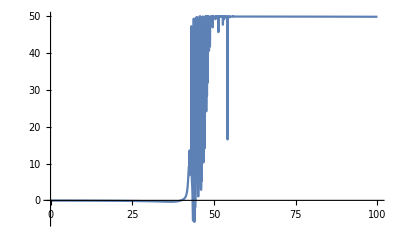

```mathematica
Plot[Evaluate[mssFake/Hfake^2/.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}],{t,0,tEnd},PlotRange->Automatic]
```

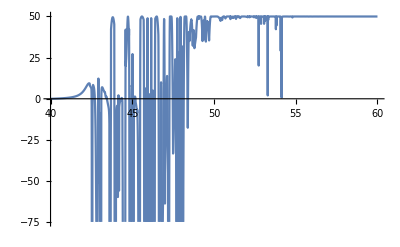

```mathematica
Plot[Evaluate[(mssFake-wVecFake.Gfake.wVecFake)/Hfake^2/.{Σ->Σval,Subscript[C, 1]->C1val,Subscript[C, 2]->C2val,Subscript[C, 3]->C3val,Λ->Λval,ξ->ξval}],{t,tEnd*0.4,tEnd*0.6},PlotRange->Automatic]
```